# Algorytm

## Wczytanie danych

```mathematica
allFiles4 =FileNames["PD_4_*.csv"]
allFiles8 =FileNames["PD_8_*.csv"]
allFiles16 =FileNames["PD_16_*.csv"]
```

{PD_4_01.csv,PD_4_02.csv,PD_4_03.csv,PD_4_04.csv,PD_4_05.csv,PD_4_06.csv,PD_4_07.csv,PD_4_08.csv,PD_4_09.csv,PD_4_10.csv,PD_4_11.csv,PD_4_12.csv,PD_4_13.csv,PD_4_14.csv,PD_4_15.csv,PD_4_16.csv,PD_4_17.csv,PD_4_18.csv,PD_4_19.csv,PD_4_20.csv}

{PD_8_01.csv,PD_8_02.csv,PD_8_03.csv,PD_8_04.csv,PD_8_05.csv,PD_8_06.csv,PD_8_07.csv,PD_8_08.csv,PD_8_09.csv,PD_8_10.csv,PD_8_11.csv,PD_8_12.csv,PD_8_13.csv,PD_8_14.csv,PD_8_15.csv,PD_8_16.csv,PD_8_17.csv,PD_8_18.csv,PD_8_19.csv,PD_8_20.csv}

{PD_16_01.csv,PD_16_02.csv,PD_16_03.csv,PD_16_04.csv,PD_16_05.csv,PD_16_06.csv,PD_16_07.csv,PD_16_08.csv,PD_16_09.csv,PD_16_10.csv,PD_16_11.csv,PD_16_12.csv,PD_16_13.csv,PD_16_14.csv,PD_16_15.csv,PD_16_16.csv,PD_16_17.csv,PD_16_18.csv,PD_16_19.csv,PD_16_20.csv}

## Proste wykresy

```mathematica
makePlot[s_]:=ListLinePlot[Rest@Import[s],PlotRange->{0,1},PlotLabel->s]
```

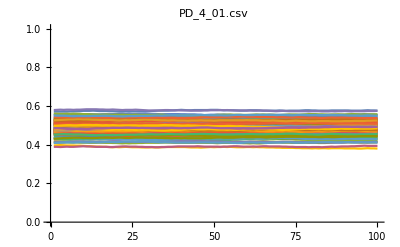
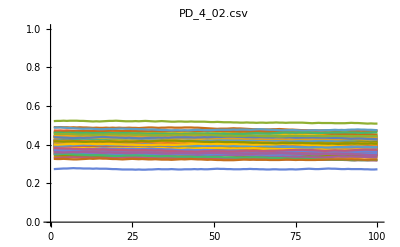
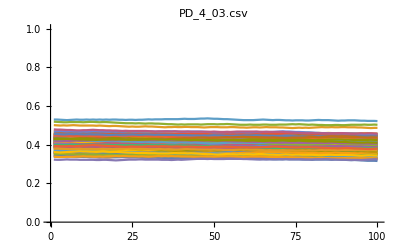
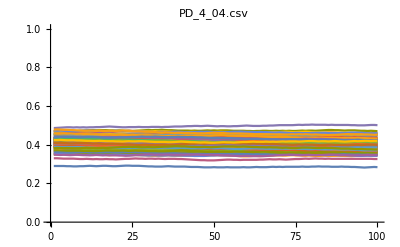
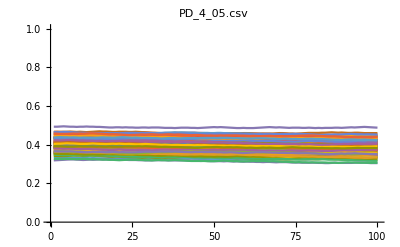
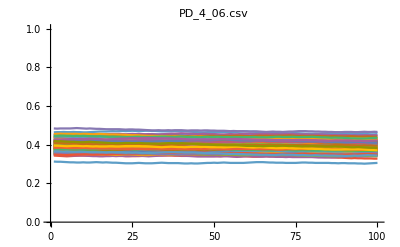
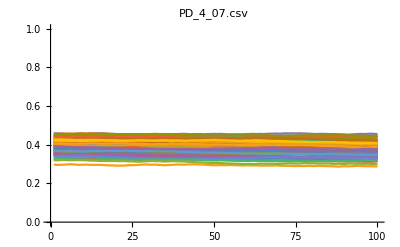
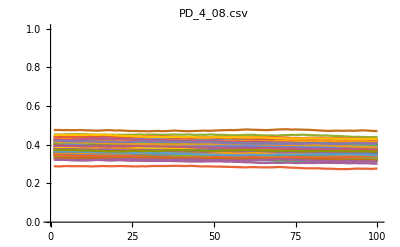

```mathematica
makePlot/@allFiles
```

## Standardowe wykresy do pracy

```mathematica
makeMean[s_]:=Mean[Flatten@Rest@Import[s]]
```

```mathematica
updateMakeMean[v_]:=Transpose[{Range[1,1.95,0.05],makeMean/@v}]
```

```mathematica
fig4=ListLinePlot[updateMakeMean[allFiles4],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic}];
fig8=ListLinePlot[updateMakeMean[allFiles8],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1,PlotStyle->Orange];
fig16=ListLinePlot[updateMakeMean[allFiles16],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1,PlotStyle->Cyan];
```

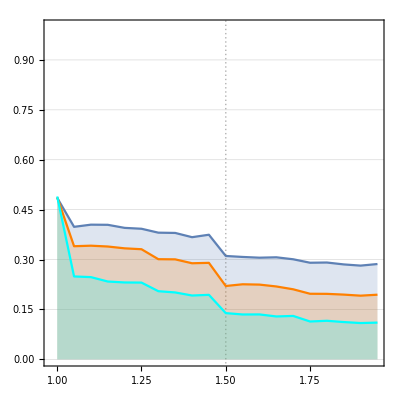

```mathematica
Show[fig4, fig8, fig16]
```

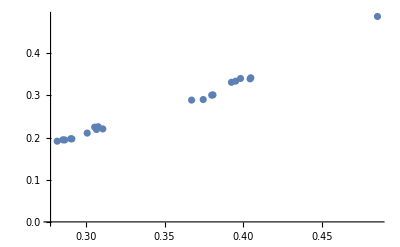

```mathematica
ListPlot[Transpose[{(makeMean/@allFiles4),(makeMean/@allFiles8)}]]
```

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
```